```mathematica
f[a1_,b1_,e1_,x_,y_, z_]=a1*x-b1*x*z-x*x-e1*x*y
```

a1 x-x^2-e1 x y-b1 x z

```mathematica
g[a2_,b2_,e2_,x_,y_, z_]=a2*y-b2*y*z-y*y-e2*x*y
```

a2 y-e2 x y-y^2-b2 y z

```mathematica
k[d1_,d2_,x_, y_, z_]= -z+d1*x*z+d2*y*z-z*z
```

-z+d1 x z+d2 y z-z^2

```mathematica
Clear[a1]
```

```mathematica
Solve[{f[a1,b1,e1, x, y, z]==0, g[ a2,b2,e2,x, y, z]==0, k[d1,d2,x, y, z]==0}, {x, y, z}]
```

{{x→0,y→0,z→0},{x→a1,y→0,z→0},{x→-(-a1-b1)/(1+b1 d1),z→-(1-a1 d1)/(1+b1 d1),y→0},{x→-(a1-a2 e1)/(-1+e1 e2),y→-(a2-a1 e2)/(-1+e1 e2),z→0},{x→-(a1+b1-a2 b1 d2+a1 b2 d2-a2 e1-b2 e1)/(-1-b1 d1-b2 d2+b2 d1 e1+b1 d2 e2+e1 e2),y→-(a2+b2+a2 b1 d1-a1 b2 d1-a1 e2-b1 e2)/(-1-b1 d1-b2 d2+b2 d1 e1+b1 d2 e2+e1 e2),z→-(-1+a1 d1+a2 d2-a2 d1 e1-a1 d2 e2+e1 e2)/(-1-b1 d1-b2 d2+b2 d1 e1+b1 d2 e2+e1 e2)},{y→a2,x→0,z→0},{y→-(-a2-b2)/(1+b2 d2),z→-(1-a2 d2)/(1+b2 d2),x→0},{z→-1,x→0,y→0}}

```mathematica
B1X[a1_,a2_, e1_, e2_]=-(a1-a2 e1)/(-1+e1 e2);
B1Y[a1_, a2_, e1_, e2_] = -(a2-a1 e2)/(-1+e1 e2);
B2Y[a2_,b2_,d2_]=-(-a2-b2)/(1+b2 d2);
B2Z[a2_, b2_, d2_] = -(1-a2 d2)/(1+b2 d2);
B3X[a1_,b1_, d1_]=-(-a1-b1)/(1+b1 d1);
B3Z[a1_, b1_, d1_]=-(1-a1 d1)/(1+b1 d1);
MX[a1_,a2_,b1_,b2_,e1_,e2_,d1_,d2_]=-(a1+b1-a2 b1 d2+a1 b2 d2-a2 e1-b2 e1)/(-1-b1 d1-b2 d2+b2 d1 e1+b1 d2 e2+e1 e2);
MY[a1_,a2_,b1_,b2_,e1_,e2_,d1_,d2_]=-(a2+b2+a2 b1 d1-a1 b2 d1-a1 e2-b1 e2)/(-1-b1 d1-b2 d2+b2 d1 e1+b1 d2 e2+e1 e2);
MZ[a1_,a2_,b1_,b2_,e1_,e2_,d1_,d2_]=-(-1+a1 d1+a2 d2-a2 d1 e1-a1 d2 e2+e1 e2)/(-1-b1 d1-b2 d2+b2 d1 e1+b1 d2 e2+e1 e2);
```

```mathematica
a1p=2.4; b1p=4;b2p=10;d1p=0.25;d2p=4;e1p=6;e2p=1;
```

```mathematica
k[d1p, d2p, x, y, z]
```

-z+0.25 x z+4 y z-z^2

```mathematica
B1X[a1p,a2, e1p, e2p]
B1Y[a1p, a2, e1p, e2p] 
B2Y[a2,b2p,d2p]
B2Z[a2, b2p, d2p] 
B3X[a1p,b1p, d1p]
B3Z[a1p, b1p, d1p]
MX[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]
MY[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]
MZ[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]
```

1/5 (-2.4+6 a2)

1/5 (2.4-a2)

(10+a2)/41

1/41 (-1+4 a2)

3.2

-0.2

0.2 (42.4-22 a2)

0.2 (-2.4+2. a2)

0.2 (-4.+2.5 a2)

```mathematica
Simplify[2*(106-55*a2)/25-0.2 (-39.6-22 a2)]
```

16.4+0. a2

```mathematica
Reduce[B1X[a1p,a2, e1p, e2p]>0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a2>0.4

```mathematica
Reduce[B1Y[a1p,a2, e1p, e2p]>0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a2<2.4

```mathematica
Reduce[B2Y[a2,b2p, d2p]>0]
```

a2>-10

```mathematica
Reduce[B2Z[a2,b2p, d2p]>0]
```

a2>1/4

```mathematica
Reduce[MX[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]>0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a2<1.92727

```mathematica
Reduce[MY[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]>0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a2>1.2

```mathematica
Reduce[MZ[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]>0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a2>1.6

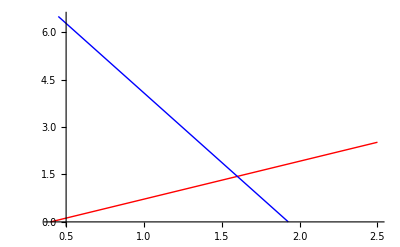

```mathematica
Plot[{B1X[a1p,a2, e1p, e2p],MX[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]},{a2,0.4,2.5}, PlotStyle->{Red, Blue}, PlotRange->{0, 6.5}]
```

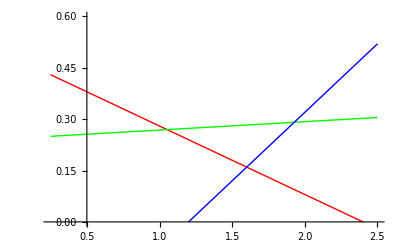

```mathematica
Plot[{B1Y[a1p,a2, e1p, e2p],B2Y[a2,b2p,d2p],MY[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]},{a2,0.25,2.5}, PlotStyle->{Red,Green, Blue}, PlotRange->{0, 0.6}]
```

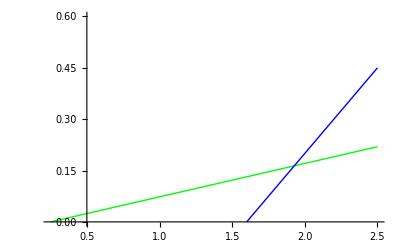

```mathematica
Plot[{B2Z[a2,b2p,d2p],MZ[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]},{a2,0.25,2.5}, PlotStyle->{Green, Blue}, PlotRange->{0, 0.6}]
```

```mathematica
fx[x_,y_, z_]=D[f[a1p,b1p,e1p,x,y, z],x];
```

```mathematica
fy[x_,y_, z_]=D[f[a1p,b1p,e1p,x,y, z],y];
```

```mathematica
fz[x_,y_, z_]=D[f[a1p,b1p,e1p,x,y, z],z];
```

```mathematica
gx[a2_,x_,y_, z_]=D[g[a2,b2p,e2p,x,y, z],x];
```

```mathematica
gy[a2_,x_,y_, z_]=D[g[a2,b2p,e2p,x,y, z],y];
```

```mathematica
gz[a2_,x_,y_, z_]=D[g[a2,b2p,e2p,x,y, z],z];
```

```mathematica
kx[x_,y_, z_]=D[k[d1p,d2p,x, y, z],x];
```

```mathematica
ky[x_,y_, z_]=D[k[d1p,d2p,x, y, z],y];
```

```mathematica
kz[x_,y_, z_]=D[k[d1p,d2p,x, y, z],z];
```

```mathematica
J[a2_, x_, y_, z_]= {{fx[x, y, z],fy[x, y, z], fz[ x, y, z]}, {gx[a2,x,y, z], gy[a2,x,y, z], gz[a2,x,y, z]}, {kx[x,y, z], ky[x,y, z], kz[x,y, z]}}
```

{{2.4-2 x-6 y-4 z,-6 x,-4 x},{-y,a2-x-2 y-10 z,-10 y},{0.25 z,4 z,-1+0.25 x+4 y-2 z}}

```mathematica
MatrixForm[J[a1, x, y, z]]
```

(2.4-2 x-6 y-4 z | -6 x | -4 x
-y | a1-x-2 y-10 z | -10 y
0.25 z | 4 z | -1+0.25 x+4 y-2 z)

```mathematica
Eigs[a2_, x_, y_, z_] = Eigenvalues[J[a2, x, y, z]]
```

{Root[2.4 a2-2.4 x-2.6 a2 x+2.6 x^2+0.5 a2 x^2-0.5 x^3-4.8 y-15.6 a2 y+14.8 x y+9.5 a2 x y-9. x^2 y+31.2 y^2+24 a2 y^2-19. x y^2-48 y^3-24. z+0.8 a2 z+25.2 x z-4. a2 x z-1. x^2 z+58.4 y z+4 a2 y z-54. x y z-8 y^2 z-8. z^2-8 a2 z^2+48. x z^2+136 y z^2+80 z^3+(-2.4+1.4 a2+1.2 x-1.75 a2 x+1.25 x^2+12.8 y-2 a2 y-10. x y-20 y^2-14.8 z-6 a2 z+27.5 x z+68 y z+68 z^2) #1+(-1.4-a2+2.75 x+4 y+16 z) #1^2+#1^3&,1],Root[2.4 a2-2.4 x-2.6 a2 x+2.6 x^2+0.5 a2 x^2-0.5 x^3-4.8 y-15.6 a2 y+14.8 x y+9.5 a2 x y-9. x^2 y+31.2 y^2+24 a2 y^2-19. x y^2-48 y^3-24. z+0.8 a2 z+25.2 x z-4. a2 x z-1. x^2 z+58.4 y z+4 a2 y z-54. x y z-8 y^2 z-8. z^2-8 a2 z^2+48. x z^2+136 y z^2+80 z^3+(-2.4+1.4 a2+1.2 x-1.75 a2 x+1.25 x^2+12.8 y-2 a2 y-10. x y-20 y^2-14.8 z-6 a2 z+27.5 x z+68 y z+68 z^2) #1+(-1.4-a2+2.75 x+4 y+16 z) #1^2+#1^3&,2],Root[2.4 a2-2.4 x-2.6 a2 x+2.6 x^2+0.5 a2 x^2-0.5 x^3-4.8 y-15.6 a2 y+14.8 x y+9.5 a2 x y-9. x^2 y+31.2 y^2+24 a2 y^2-19. x y^2-48 y^3-24. z+0.8 a2 z+25.2 x z-4. a2 x z-1. x^2 z+58.4 y z+4 a2 y z-54. x y z-8 y^2 z-8. z^2-8 a2 z^2+48. x z^2+136 y z^2+80 z^3+(-2.4+1.4 a2+1.2 x-1.75 a2 x+1.25 x^2+12.8 y-2 a2 y-10. x y-20 y^2-14.8 z-6 a2 z+27.5 x z+68 y z+68 z^2) #1+(-1.4-a2+2.75 x+4 y+16 z) #1^2+#1^3&,3]}

```mathematica
Eig1[a2_] = Eigs[a2, MX[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p], MY[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p], MZ[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]][[1]];
Eig2[a2_] = Eigs[a2, MX[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p], MY[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p], MZ[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]][[2]];
Eig3[a2_] = Eigs[a2, MX[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p], MY[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p], MZ[a1p,a2,b1p,b2p,e1p,e2p,d1p,d2p]][[3]];
```

```mathematica
Plot[{Eigs[a2, 0, a2p, 0][[2]]}, {a1, 5.7, 5.738}]
```

-Graphics-

```mathematica
Eigs[1, 0, a2p, 0]
```

{Root[2.4-20.4 a2p+55.2 a2p^2-48 a2p^3+(-1.+10.8 a2p-20 a2p^2) #1+(-2.4+4 a2p) #1^2+#1^3&,1],Root[2.4-20.4 a2p+55.2 a2p^2-48 a2p^3+(-1.+10.8 a2p-20 a2p^2) #1+(-2.4+4 a2p) #1^2+#1^3&,2],Root[2.4-20.4 a2p+55.2 a2p^2-48 a2p^3+(-1.+10.8 a2p-20 a2p^2) #1+(-2.4+4 a2p) #1^2+#1^3&,3]}

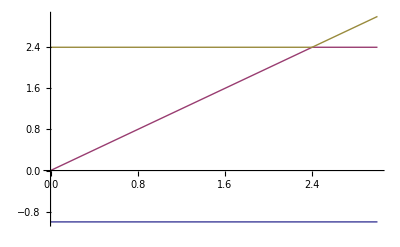

```mathematica
Plot[{Eigs[a2, 0, 0, 0][[1]],Eigs[a2, 0, 0, 0][[2]], Eigs[a2, 0, 0, 0][[3]]}, {a2, 0, 3}]
```

```mathematica
Eigs[a1, a1, 0, 0]
```

{Root[0. a1+0. a1^2+0. a1^3+(-2.4+2.6 a1-0.5 a1^2) #1+(-1.4+1.75 a1) #1^2+#1^3&,1],Root[0. a1+0. a1^2+0. a1^3+(-2.4+2.6 a1-0.5 a1^2) #1+(-1.4+1.75 a1) #1^2+#1^3&,2],Root[0. a1+0. a1^2+0. a1^3+(-2.4+2.6 a1-0.5 a1^2) #1+(-1.4+1.75 a1) #1^2+#1^3&,3]}

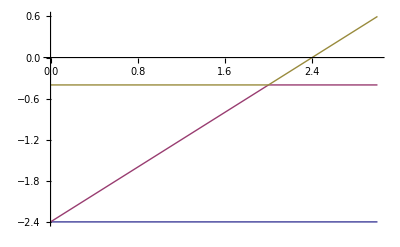

```mathematica
Plot[{Eigs[a2, a1p, 0, 0][[1]], Eigs[a2, a1p, 0, 0][[2]],Eigs[a2, a1p, 0, 0][[3]]}, {a2, 0, 3}]
```

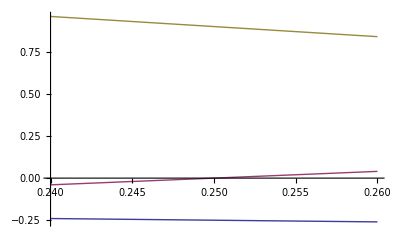

```mathematica
Plot[{Eigs[a2, 0, a2, 0][[1]], Eigs[a2, 0, a2, 0][[2]],Eigs[a2, 0, a2, 0][[3]]}, {a2, 0.24, 0.26}]
```

```mathematica
B1X[a1p,a2, e1p, e2p]
B1Y[a1p,a2, e1p, e2p]
```

1/5 (-2.4+6 a2)

1/5 (2.4-a2)

```mathematica
a2p=2.3;
Eigs[a2p, B1X[a1p,a2p, e1p, e2p], B1Y[a1p,a2p, e1p, e2p], 0]
```

{-2.39519,-0.35,0.0951907}

```mathematica
Eigensystem[J[a2p, B1X[a1p,a2p, e1p, e2p], B1Y[a1p,a2p, e1p, e2p], 0]]
```

{{-2.39519,-0.35,0.0951907},{{-0.999965,-0.00842008,0.},{-0.987071,0.0349777,0.15642},{0.98526,-0.171066,0.}}}

```mathematica
Plot[{Eigs[a2, 0, 0, 0][[1]],Eigs[a2, 0, 0, 0][[2]], Eigs[a2, 0, 0, 0][[3]]}, {a2, 0, 3}]
```

-Graphics-

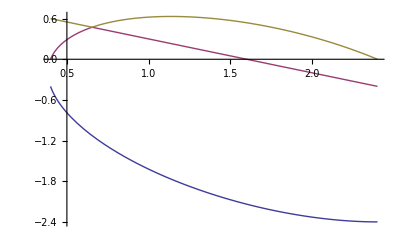

```mathematica
Plot[{Eigs[a2, B1X[a1p,a2, e1p, e2p], B1Y[a1p,a2, e1p, e2p], 0][[1]],Eigs[a2, B1X[a1p,a2, e1p, e2p], B1Y[a1p,a2, e1p, e2p], 0][[2]], Eigs[a2, B1X[a1p,a2, e1p, e2p], B1Y[a1p,a2, e1p, e2p], 0][[3]]}, {a2, 0.4, 2.4}]
```

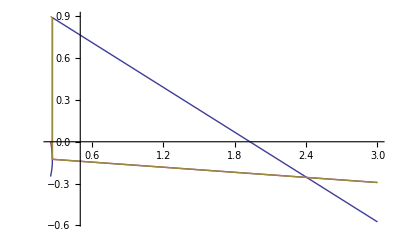

```mathematica
Plot[{Re[Eigs[a2, 0, B2Y[a2,b2p,d2p], B2Z[a2,b2p,d2p]][[1]]], Re[Eigs[a2, 0, B2Y[a2,b2p,d2p], B2Z[a2,b2p,d2p]][[2]]], Re[Eigs[a2, 0, B2Y[a2,b2p,d2p], B2Z[a2,b2p,d2p]][[3]]]}, {a2,0.25, 3}]
```

```mathematica
Re[Eigs[a1, 0, 1/d2p, B2Z[a2p,b2p,d2p]][[2]]], Re[Eigs[a1, 0, 1/d2p, B2Z[a2p,b2p,d2p]][[3]]]
```

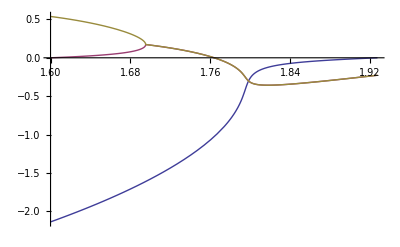

```mathematica
Plot[{Re[Eig1[a2]], Re[Eig2[a2]], Re[Eig3[a2]]},{a2,1.6,1.92727}]
```